```mathematica
getstdx[V1_, V2_,x1startest_, x1endest_,precision_]:=Module[{x1,x2,x3,x1start, x1end,x1new,area},
x1start=x1startest;
x1end=x1endest;
While[x1end-x1start>precision,
x1new = (x1start+x1end)/2;
x2=a/.FindRoot[Integrate[ⅇ^(x^2),{x,x1new,a}]==V1,{a,x1new/2}];
area=NIntegrate[ⅇ^(x^2),{x,x2,-(x1new+x2)}];
If[area>V2,x1start=x1new,x1end=x1new]
];
x1=(x1start+x1end)/2;
x2=a/.FindRoot[Integrate[ⅇ^(x^2),{x,x1,a}]==V1,{a,x1/2}];
x3=-(x1+x2);
Return[{x1, x2, x3}]
];

density[val_, ϵ_]:=If[Abs[val]<ϵ,Return[ⅇ^(val^2)],Return[ⅇ^(ϵ(2Abs[val]-ϵ))]];

pdiff[V1_,V2_,ϵ_,precision_]:=
Module[{x1,x2,x3,y1,y2,diff,x1start,x1end,x1new,area,smoothvol,values},
(*Volume of the smooth region*)
smoothvol = Integrate[ⅇ^(x^2),{x, -ϵ, ϵ}];

(*Computes the position of the isoperimetric triple interval*)
If[V1+V2≤smoothvol,
y1 =a/.FindRoot[Integrate[ⅇ^(x^2),{x,0,a}]==V1/2,{a,0}];
y2=a/.FindRoot[Integrate[ⅇ^(x^2),{x,y1,a}]==V2/2,{a,y1}];,
If[V1≤smoothvol,
y1 =a/.FindRoot[Integrate[ⅇ^(x^2),{x,0,a}]==V1/2,{a,0}];
y2=a/.FindRoot[Integrate[ⅇ^(ϵ(2x-ϵ)),{x,ϵ,a}]==(V2+V1-smoothvol)/2,{a,ϵ}];,

y1 =a/.FindRoot[Integrate[ⅇ^(ϵ(2x-ϵ)),{x,ϵ,a}]==(V1-smoothvol)/2,{a,ϵ}];
y2=a/.FindRoot[Integrate[ⅇ^(ϵ(2x-ϵ)),{x,y1,a}]==V2/2,{a,y1}];
];
];

(*Computes the position of the isoperimetric double interval*)
If[V1≥smoothvol/2,
x1 =-a/.FindRoot[Integrate[ⅇ^(ϵ(2x-ϵ)),{x,ϵ,a}]==(V1-smoothvol)/2,{a,ϵ}];
x2=-a/.FindRoot[Integrate[ⅇ^(ϵ(2x-ϵ)),{x,ϵ,a}]==(V2-smoothvol)/2,{a,-x1}];
x3=-(x1+x2);,
If[V2≤ smoothvol/2,
values=getstdx[V1, V2, -y2, -y1,precision];
x1=values[[1]];
x2=values[[2]];
x3=values[[3]];,

x1=a/.FindRoot[Integrate[ⅇ^(x^2), {x, a, -ϵ-a}]==V1,{a, 0}];
x2=-ϵ-x1;
x3=a/.FindRoot[Integrate[ⅇ^(x^2), {x, x2, ϵ}]+Integrate[ⅇ^(ϵ(2x-ϵ)),{x,ϵ,a}]==V2,{a,ϵ}];
];
];
Print["x1=",x1," x2=", x2," x3=", x3,"y1=",y1," y2=",y2];
diff=2 density[y1,ϵ]+2 density[y2,ϵ]-density[x1,ϵ]-density[x2,ϵ]-density[x3,ϵ];
Return[diff];
]
```

```mathematica
table[range_,blocks_,precision_,ϵ_]:=
Module[{g},
g=Table[0,{i,blocks},{j,blocks}];
For[i=1,i≤blocks,i++,
For[j=i,j≤blocks,j++,
g[[i,j]]=pdiff[i*range/blocks,j*range/blocks,ϵ,precision];
]
];
Return[g];
]
```

```mathematica
tabletest[range_,blocks_,precision_,ϵ_]:=
Module[{g},
g=Table[pdiff[i*range/blocks,j*range/blocks,ϵ,precision],{i,blocks},{j,blocks}];
Return[g];
]
```

```mathematica
g=tabletest[1000, 5, 0.00001,3]
```

x1=-2.61873 x2=0.00439132 x3=2.61434y1=2.46746 y2=2.61874

x1=-2.61888 x2=-0.139283 x3=2.75817y1=2.46746 y2=2.70231

x1=-2.61897 x2=-0.220902 x3=2.83987y1=2.46746 y2=2.75971

x1=-2.61903 x2=-0.275002 x3=2.89403y1=2.46746 y2=2.80325

x1=-2.61908 x2=-0.316694 x3=2.93577y1=2.46746 y2=2.83823

x1=-2.70231 x2=2.46747 x3=0.234835y1=2.61874 y2=2.70231

x1=-2.75971 x2=0.00873545 x3=2.75097y1=2.61874 y2=2.75971

x1=-2.75975 x2=-0.0745643 x3=2.83432y1=2.61874 y2=2.80325

x1=-2.75978 x2=-0.132829 x3=2.89261y1=2.61874 y2=2.83823

x1=-2.7598 x2=-0.179616 x3=2.93942y1=2.61874 y2=2.8674

x1=-2.75971 x2=2.61874 x3=0.140968y1=2.70231 y2=2.75971

x1=-2.80325 x2=2.46748 x3=0.33577y1=2.70231 y2=2.80325

x1=-2.83822 x2=0.0130701 x3=2.82515y1=2.70231 y2=2.83823

x1=-2.83825 x2=-0.0543278 x3=2.89257y1=2.70231 y2=2.8674

x1=-2.83826 x2=-0.100908 x3=2.93917y1=2.70231 y2=2.89238

x1=-2.80325 x2=2.70231 x3=0.100937y1=2.75971 y2=2.80325

x1=-2.83822 x2=2.61875 x3=0.219472y1=2.75971 y2=2.83823

x1=-2.8674 x2=2.46749 x3=0.399905y1=2.75971 y2=2.8674

x1=-2.89238 x2=0.017399 x3=2.87498y1=2.75971 y2=2.89238

x1=-2.89239 x2=-0.0446292 x3=2.93702y1=2.75971 y2=2.91421

x1=-2.83822 x2=2.75972 x3=0.0785032y1=2.80325 y2=2.83823

x1=-2.86739 x2=2.70232 x3=0.165076y1=2.80325 y2=2.8674

x1=-2.89238 x2=2.61875 x3=0.273633y1=2.80325 y2=2.89238

x1=-2.91421 x2=2.4675 x3=0.446705y1=2.80325 y2=2.91421

x1=-2.93357 x2=0.0217238 x3=2.91184y1=2.80325 y2=2.93357

{{902.065,883.158,808.108,762.356,695.208},{2944.71,1997.02,1962.46,1869.15,1659.3},{4046.15,5113.07,3191.91,2956.49,2764.88},{5162.91,6259.86,7340.93,4470.48,3943.68},{6293.62,7410.75,8519.46,9610.57,5824.65}}

```mathematica
Transpose[g]
```

Transpose::nmtx: The first two levels of {{902.065,883.158,808.108,762.356,695.208},{1997.02,1962.46,1869.15,1659.3},{3191.91,2956.49,2764.88},{4470.48,3943.68},{5824.65}} cannot be transposed.

Transpose[{{902.065,883.158,808.108,762.356,695.208},{1997.02,1962.46,1869.15,1659.3},{3191.91,2956.49,2764.88},{4470.48,3943.68},{5824.65}}]

```mathematica
Length[g]
```

10

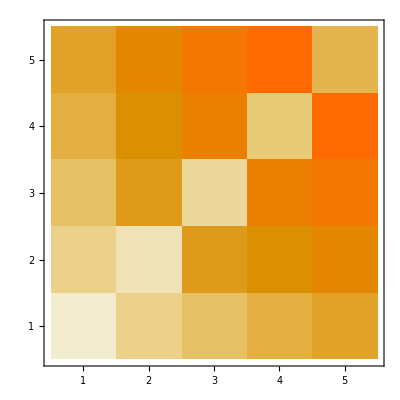

```mathematica
MatrixPlot[g+Transpose[g]-IdentityMatrix[5]*Diagonal[g], DataReversed->True]
```